```mathematica
Table[allGraphs3[k,"graph"]->allGraphs3[k,"colofour"],{k,Keys[allGraphs3]}]
```

{-Graphics-→v123+v12x3+v13x2+v1x23+v1x2x3,-Graphics-→v13x2+v1x23+v1x2x3,-Graphics-→v1x23+v1x2x3,-Graphics-→v1x2x3,-Graphics-→v1x23,-Graphics-→v13x2,-Graphics-→v13x2+v1x2x3,-Graphics-→v123+v12x3,-Graphics-→v12x3,-Graphics-→v123,-Graphics-→v12x3+v1x23+v1x2x3,-Graphics-→v12x3+v1x2x3,-Graphics-→v123+v13x2,-Graphics-→v12x3+v13x2+v1x2x3,-Graphics-→v123+v1x23}

```mathematica
allGraphs3[1]
```

<|signature→1,matrix→{{2,0,0},{0,2,1},{0,1,2}},graph→-Graphics-,vertexsets→{{1},{2},{3}},vertices→{1,2,3},edges→{2<->3},relations→{x1==x10+x22,x1==x16+x4,x1==x0-x2},links→{},parents→{0},children→{{10,22},{4,16}},comp→Greater,compwhy→This is a planar contraction,colofour→v12x3+v13x2+v1x2x3,colortable→{{v12x3,v13x2+v1x2x3},{v13x2,v12x3+v1x2x3},{0,v12x3+v13x2+v1x2x3}},colofournull→p1x23,colofourrealnull→-n1x23+n1x2x3|>

```mathematica
repFullEmbed
```

{v1x2x3x4x5→0,v1x2x3x45→10,v1x2x35x4→6,v1x2x34x5→20,v1x2x345→14,v1x25x3x4→11,v1x25x34→31,v1x24x3x5→6,v1x24x35→0,v1x245x3→10,v1x23x4x5→10,v1x23x45→14,v1x235x4→10,v1x234x5→14,v1x2345→11,v15x2x3x4→11,v15x2x34→29,v15x24x3→8,v15x23x4→16,v15x234→11,v14x2x3x5→9,v14x2x35→3,v14x25x3→8,v14x23x5→8,v14x235→4,v145x2x3→20,v145x23→12,v13x2x4x5→9,v13x2x45→8,v13x25x4→8,v13x24x5→3,v13x245→4,v135x2x4→13,v135x24→5,v134x2x5→7,v134x25→9,v1345x2→16,v12x3x4x5→11,v12x3x45→16,v12x35x4→8,v12x34x5→29,v12x345→11,v125x3x4→21,v125x34→26,v124x3x5→13,v124x35→5,v1245x3→18,v123x4x5→20,v123x45→12,v1235x4→18,v1234x5→16,v12345→16}

```mathematica
ZetaFunction[allGraphs3[1,"Graph"]]
```

VertexList::graph: A graph object is expected at position 1 in VertexList[Missing[KeyAbsent,Graph]].

Table::iterb: Iterator {v,VertexList[Missing[KeyAbsent,Graph]]} does not have appropriate bounds.

GraphComplement::graph: A graph object is expected at position 1 in GraphComplement[Missing[KeyAbsent,Graph]].

EdgeList::graph: A graph object is expected at position 1 in EdgeList[GraphComplement[Missing[KeyAbsent,Graph]]].

Part::partw: Part 2 of GraphComplement[Missing[KeyAbsent,Graph]] does not exist.

Part::pkspec1: The expression pos1 cannot be used as a part specification.

Part::pkspec1: The expression pos2 cannot be used as a part specification.

Part::pkspec1: The expression pos1 cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Set::pkspec1: The expression pos1 cannot be used as a part specification.

Delete::pkspec: The expression pos2 cannot be used as a part specification. Use Key[pos2] instead.

EdgeAdd::graph: A graph object is expected at position 1 in EdgeAdd[Missing[KeyAbsent,Graph],GraphComplement[Missing[KeyAbsent,Graph]]].

GraphComplement::graph: A graph object is expected at position 1 in GraphComplement[EdgeAdd[Missing[KeyAbsent,Graph],GraphComplement[Missing[KeyAbsent,Graph]]]].

EdgeList::graph: A graph object is expected at position 1 in EdgeList[GraphComplement[EdgeAdd[Missing[KeyAbsent,Graph],GraphComplement[Missing[KeyAbsent,Graph]]]]].

Part::partw: Part 2 of GraphComplement[EdgeAdd[Missing[KeyAbsent,Graph],GraphComplement[Missing[KeyAbsent,Graph]]]] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Set::pkspec1: The expression pos1 cannot be used as a part specification.

Delete::pkspec: The expression pos2 cannot be used as a part specification. Use Key[pos2] instead.

EdgeAdd::graph: A graph object is expected at position 1 in EdgeAdd[EdgeAdd[Missing[KeyAbsent,Graph],GraphComplement[Missing[KeyAbsent,Graph]]],GraphComplement[EdgeAdd[Missing[KeyAbsent,Graph],GraphComplement[Missing[KeyAbsent,Graph]]]]].

GraphComplement::graph: A graph object is expected at position 1 in GraphComplement[EdgeAdd[EdgeAdd[Missing[KeyAbsent,Graph],GraphComplement[Missing[KeyAbsent,Graph]]],GraphComplement[EdgeAdd[Missing[KeyAbsent,Graph],GraphComplement[Missing[KeyAbsent,Graph]]]]]].

General::stop: Further output of GraphComplement::graph will be suppressed during this calculation.

EdgeList::graph: A graph object is expected at position 1 in EdgeList[GraphComplement[EdgeAdd[EdgeAdd[Missing[KeyAbsent,Graph],GraphComplement[Missing[KeyAbsent,Graph]]],GraphComplement[EdgeAdd[Missing[KeyAbsent,Graph],GraphComplement[Missing[KeyAbsent,Graph]]]]]]].

General::stop: Further output of EdgeList::graph will be suppressed during this calculation.

Set::pkspec1: The expression pos1 cannot be used as a part specification.

General::stop: Further output of Set::pkspec1 will be suppressed during this calculation.

Delete::pkspec: The expression pos2 cannot be used as a part specification. Use Key[pos2] instead.

General::stop: Further output of Delete::pkspec will be suppressed during this calculation.

EdgeAdd::graph: A graph object is expected at position 1 in EdgeAdd[EdgeAdd[EdgeAdd[Missing[KeyAbsent,Graph],GraphComplement[Missing[KeyAbsent,Graph]]],GraphComplement[EdgeAdd[Missing[KeyAbsent,Graph],GraphComplement[Missing[KeyAbsent,Graph]]]]],GraphComplement[EdgeAdd[EdgeAdd[Missing[KeyAbsent,Graph],GraphComplement[Missing[KeyAbsent,Graph]]],GraphComplement[EdgeAdd[Missing[KeyAbsent,Graph],GraphComplement[Missing[KeyAbsent,Graph]]]]]]].

General::stop: Further output of EdgeAdd::graph will be suppressed during this calculation.

$Aborted

```mathematica
Keys[allBases]
```

Keys::invrl: The argument C is not a valid Association or a list of rules.

Keys[{C,E,G,F,T}]

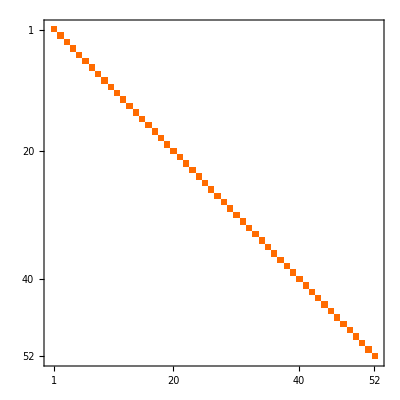
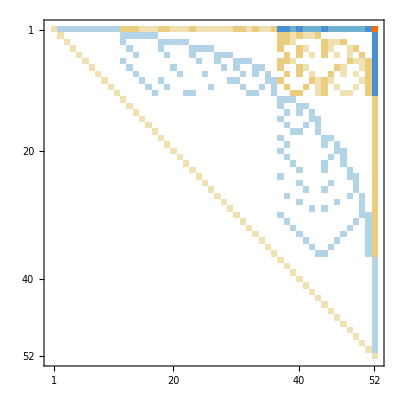
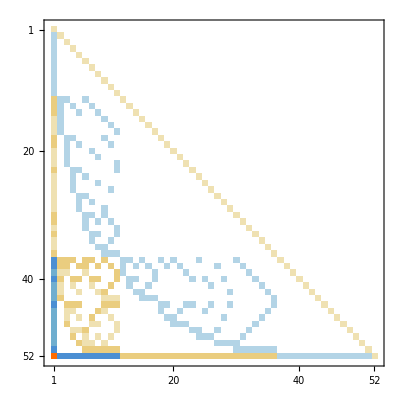
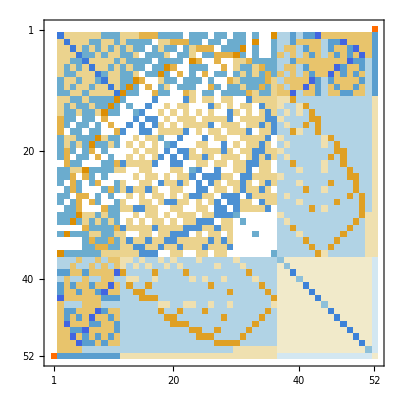
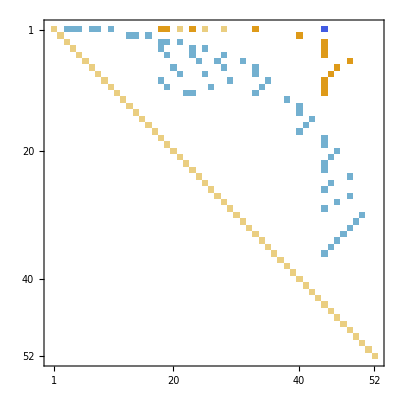
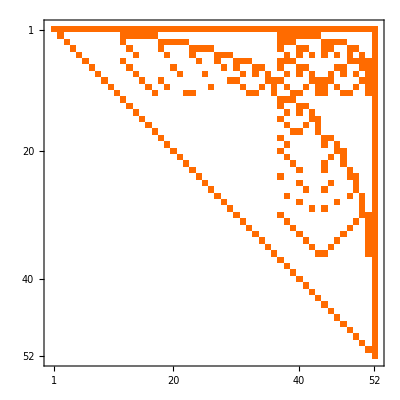
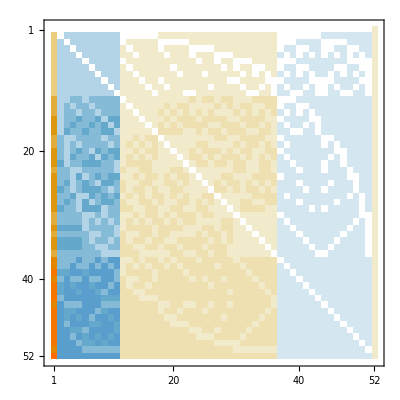
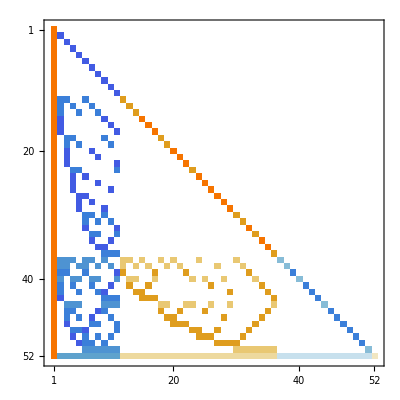
( | C | E | G | F | T
C | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
E | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
G | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
F | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
T | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-)

```mathematica
MatrixForm[Table[ConversionMatrix[from,to]//MatrixPlot,{from,allBases},{to,allBases}], TableHeadings->{allBases, allBases}]
```

```mathematica
Keys  [allGraphs6[0]]
```

{signature,matrix,graph,vertexsets,vertices,edges,relations,links,parents,children,comp,compwhy,colofour,colortable,colofourrealnull,colofournull,colofourgenerator}

```mathematica
Bases["G","AtomKeys"]
```

{29524,9841,22963,27337,28795,29281,29443,29497,29515,29521,29523,3037,7573,9085,9832,9838,9840,20767,22231,22882,22936,22962,26607,27094,27310,27334,28552,28714,28786,29191,29251,29280,29415,29440,29488,29511,760,2278,3036,6816,7570,9076,9828,20034,20740,22150,22854,26364,27064,28462,29160,0}

```mathematica
Map[allGraphs5[#,"colofourgenerator"]&,Bases["G","AtomKeys"]]/.RepGraph["G"]
```

{-Graphics-295240,-Graphics-98410,-Graphics-229630,-Graphics-273370,-Graphics-287950,-Graphics-292810,-Graphics-294430,-Graphics-294970,-Graphics-295150,-Graphics-295210,-Graphics-295230,-Graphics-30371,-Graphics-75731,-Graphics-90851,-Graphics-98321,-Graphics-98381,-Graphics-98401,-Graphics-207671,-Graphics-222311,-Graphics-228820,-Graphics-229360,-Graphics-229621,-Graphics-266071,-Graphics-270941,-Graphics-273100,-Graphics-273340,-Graphics-285521,-Graphics-287141,-Graphics-287861,-Graphics-291911,-Graphics-292511,-Graphics-292801,-Graphics-294151,-Graphics-294400,-Graphics-294881,-Graphics-295111,-Graphics-7608,-Graphics-22788,-Graphics-30365,-Graphics-68168,-Graphics-75703,-Graphics-90765,-Graphics-98285,-Graphics-200348,-Graphics-207403,-Graphics-221503,-Graphics-228543,-Graphics-263645,-Graphics-270643,-Graphics-284625,-Graphics-291608,-Graphics-034}

```mathematica
Map[allGraphs6[#,"colofourgenerator"]&,Bases6["G","AtomKeys"]]/.RepGraph6["G"]
```

{-Graphics-7174453,-Graphics-2391484,-Graphics-5580130,-Graphics-6643012,-Graphics-6997306,-Graphics-7115404,-Graphics-7154770,-Graphics-7167892,-Graphics-7172266,-Graphics-7173724,-Graphics-7174210,-Graphics-7174372,-Graphics-7174426,-Graphics-7174444,-Graphics-7174450,-Graphics-7174452,-Graphics-777478,-Graphics-1853482,-Graphics-2212150,-Graphics-2331706,-Graphics-2391241,-Graphics-2391403,-Graphics-2391457,-Graphics-2391475,-Graphics-2391481,-Graphics-2391483,-Graphics-5048446,-Graphics-5402902,-Graphics-5521054,-Graphics-5573569,-Graphics-5577943,-Graphics-5579401,-Graphics-5580121,-Graphics-5580127,-Graphics-5580129,-Graphics-6465856,-Graphics-6583960,-Graphics-6623329,-Graphics-6640825,-Graphics-6642283,-Graphics-6642931,-Graphics-6642985,-Graphics-6643011,-Graphics-6938256,-Graphics-6977623,-Graphics-6990745,-Graphics-6996577,-Graphics-6997063,-Graphics-6997279,-Graphics-6997303,-Graphics-7095721,-Graphics-7108843,-Graphics-7113217,-Graphics-7115161,-Graphics-7115323,-Graphics-7115395,-Graphics-7147966,-Graphics-7152502,-Graphics-7154014,-Graphics-7154761,-Graphics-7154767,-Graphics-7154769,-Graphics-7165696,-Graphics-7167160,-Graphics-7167811,-Graphics-7167865,-Graphics-7167891,-Graphics-7171536,-Graphics-7172023,-Graphics-7172239,-Graphics-7172263,-Graphics-7173481,-Graphics-7173643,-Graphics-7173715,-Graphics-7174120,-Graphics-7174180,-Graphics-7174209,-Graphics-7174344,-Graphics-7174369,-Graphics-7174417,-Graphics-7174440,-Graphics-239233,-Graphics-598063,-Graphics-717673,-Graphics-777469,-Graphics-777475,-Graphics-777477,-Graphics-1674139,-Graphics-1793701,-Graphics-1853401,-Graphics-1853455,-Graphics-1853481,-Graphics-2152371,-Graphics-2211907,-Graphics-2212123,-Graphics-2212147,-Graphics-2331463,-Graphics-2331625,-Graphics-2331697,-Graphics-2391151,-Graphics-2391211,-Graphics-2391240,-Graphics-2391375,-Graphics-2391400,-Graphics-2391448,-Graphics-2391471,-Graphics-4871209,-Graphics-4989367,-Graphics-5046259,-Graphics-5047717,-Graphics-5048445,-Graphics-5343825,-Graphics-5396341,-Graphics-5402173,-Graphics-5402899,-Graphics-5514493,-Graphics-5518867,-Graphics-5521045,-Graphics-5571373,-Graphics-5572837,-Graphics-5573568,-Graphics-5577213,-Graphics-5577940,-Graphics-5579392,-Graphics-5580117,-Graphics-6406803,-Graphics-6446173,-Graphics-6465127,-Graphics-6465829,-Graphics-6564277,-Graphics-6581773,-Graphics-6583879,-Graphics-6621061,-Graphics-6622573,-Graphics-6623328,-Graphics-6640095,-Graphics-6640798,-Graphics-6642202,-Graphics-6642903,-Graphics-6918573,-Graphics-6931695,-Graphics-6938013,-Graphics-6970819,-Graphics-6976867,-Graphics-6977620,-Graphics-6990013,-Graphics-6990718,-Graphics-6996334,-Graphics-6997033,-Graphics-7088917,-Graphics-7093453,-Graphics-7095712,-Graphics-7106647,-Graphics-7108762,-Graphics-7112974,-Graphics-7115071,-Graphics-7145689,-Graphics-7147207,-Graphics-7147965,-Graphics-7151745,-Graphics-7152499,-Graphics-7154005,-Graphics-7154757,-Graphics-7164963,-Graphics-7165669,-Graphics-7167079,-Graphics-7167783,-Graphics-7171293,-Graphics-7171993,-Graphics-7173391,-Graphics-7174089,-Graphics-59809,-Graphics-179425,-Graphics-239232,-Graphics-538257,-Graphics-598060,-Graphics-717664,-Graphics-777465,-Graphics-1614357,-Graphics-1674112,-Graphics-1793620,-Graphics-1853373,-Graphics-2152128,-Graphics-2211877,-Graphics-2331373,-Graphics-2391120,-Graphics-4812129,-Graphics-4870480,-Graphics-4987180,-Graphics-5045529,-Graphics-5337264,-Graphics-5395609,-Graphics-5512297,-Graphics-5570640,-Graphics-6387120,-Graphics-6445417,-Graphics-6562009,-Graphics-6620304,-Graphics-6911769,-Graphics-6970060,-Graphics-7086640,-Graphics-7144929,-Graphics-0}

```mathematica
Map[allGraphs6[#,"colofour"]&,Bases["C","AtomKeys"]]/.RepGraph6["C"]
```

{-Graphics-11957422+-Graphics-8768776+-Graphics-7705894+-Graphics-7233502+-Graphics-7351600+-Graphics-7174453,-Graphics-13571428+-Graphics-7725577+-Graphics-7253185+-Graphics-7371283+-Graphics-7194136,-Graphics-12495424+-Graphics-8775337+-Graphics-7240063+-Graphics-7358161+-Graphics-7181014,-Graphics-12136756+-Graphics-8770963+-Graphics-7708081+-Graphics-7235689+-Graphics-7176640,-Graphics-12017200+-Graphics-8769505+-Graphics-7706623+-Graphics-7352329+-Graphics-7175182,-Graphics-11957665+-Graphics-9300460+-Graphics-7233745+-Graphics-7351843+-Graphics-7174696,-Graphics-11957503+-Graphics-8946004+-Graphics-7705975+-Graphics-7233583+-Graphics-7174534,-Graphics-11957449+-Graphics-8827852+-Graphics-7705921+-Graphics-7351627+-Graphics-7174480,-Graphics-11957431+-Graphics-8768785+-Graphics-7883050+-Graphics-7233511+-Graphics-7174462,-Graphics-11957425+-Graphics-8768779+-Graphics-7764946+-Graphics-7351603+-Graphics-7174456,-Graphics-11957423+-Graphics-8768777+-Graphics-7705895+-Graphics-7410650+-Graphics-7174454,-Graphics-14109673+-Graphics-7259989+-Graphics-7378087+-Graphics-7200940,-Graphics-13750843+-Graphics-7727845+-Graphics-7255453+-Graphics-7196404,-Graphics-13631233+-Graphics-7726333+-Graphics-7372039+-Graphics-7194892,-Graphics-13571437+-Graphics-7902733+-Graphics-7253194+-Graphics-7194145,-Graphics-13571431+-Graphics-7784629+-Graphics-7371286+-Graphics-7194139,-Graphics-13571429+-Graphics-7725578+-Graphics-7430333+-Graphics-7194137,-Graphics-12674767+-Graphics-8777533+-Graphics-7242259+-Graphics-7183210,-Graphics-12555205+-Graphics-8776069+-Graphics-7358893+-Graphics-7181746,-Graphics-12495505+-Graphics-8952565+-Graphics-7240144+-Graphics-7181095,-Graphics-12495451+-Graphics-8834413+-Graphics-7358188+-Graphics-7181041,-Graphics-12495425+-Graphics-8775338+-Graphics-7417211+-Graphics-7181015,-Graphics-12196535+-Graphics-8771693+-Graphics-7708811+-Graphics-7177370,-Graphics-12136999+-Graphics-9302647+-Graphics-7235932+-Graphics-7176883,-Graphics-12136783+-Graphics-8830039+-Graphics-7708108+-Graphics-7176667,-Graphics-12136759+-Graphics-8770966+-Graphics-7767133+-Graphics-7176643,-Graphics-12017443+-Graphics-9301189+-Graphics-7352572+-Graphics-7175425,-Graphics-12017281+-Graphics-8946733+-Graphics-7706704+-Graphics-7175263,-Graphics-12017209+-Graphics-8769514+-Graphics-7883779+-Graphics-7175191,-Graphics-11957755+-Graphics-9477697+-Graphics-7233835+-Graphics-7174786,-Graphics-11957695+-Graphics-9359539+-Graphics-7351873+-Graphics-7174726,-Graphics-11957666+-Graphics-9300461+-Graphics-7410893+-Graphics-7174697,-Graphics-11957531+-Graphics-9005081+-Graphics-7706003+-Graphics-7174562,-Graphics-11957506+-Graphics-8946007+-Graphics-7765027+-Graphics-7174537,-Graphics-11957458+-Graphics-8827861+-Graphics-7883077+-Graphics-7174489,-Graphics-11957435+-Graphics-8768789+-Graphics-7942103+-Graphics-7174466,-Graphics-14289097+-Graphics-7262266+-Graphics-7203217,-Graphics-14169481+-Graphics-7378846+-Graphics-7201699,-Graphics-14109674+-Graphics-7437137+-Graphics-7200941,-Graphics-13810649+-Graphics-7728602+-Graphics-7197161,-Graphics-13750846+-Graphics-7786897+-Graphics-7196407,-Graphics-13631242+-Graphics-7903489+-Graphics-7194901,-Graphics-13571441+-Graphics-7961786+-Graphics-7194149,-Graphics-12734549+-Graphics-8778266+-Graphics-7183943,-Graphics-12674794+-Graphics-8836609+-Graphics-7183237,-Graphics-12555286+-Graphics-8953297+-Graphics-7181827,-Graphics-12495533+-Graphics-9011642+-Graphics-7181123,-Graphics-12196778+-Graphics-9303377+-Graphics-7177613,-Graphics-12137029+-Graphics-9361726+-Graphics-7176913,-Graphics-12017533+-Graphics-9478426+-Graphics-7175515,-Graphics-11957786+-Graphics-9536777+-Graphics-7174817,-Graphics-14348906+-Graphics-7203977}

```mathematica
RepGraph["C"]
```

{v1x2x3x4x5→-Graphics-295240,v12x3x4x5→-Graphics-492070,v13x2x4x5→-Graphics-360850,v14x2x3x5→-Graphics-317110,v15x2x3x4→-Graphics-302530,v1x23x4x5→-Graphics-297670,v1x24x3x5→-Graphics-296050,v1x25x3x4→-Graphics-295510,v1x2x34x5→-Graphics-295330,v1x2x35x4→-Graphics-295270,v1x2x3x45→-Graphics-295250,v123x4x5→-Graphics-560111,v124x3x5→-Graphics-514750,v125x3x4→-Graphics-499631,v12x34x5→-Graphics-492161,v12x35x4→-Graphics-492100,v12x3x45→-Graphics-492081,v134x2x5→-Graphics-382810,v135x2x4→-Graphics-368170,v13x24x5→-Graphics-361660,v13x25x4→-Graphics-361120,v13x2x45→-Graphics-360860,v145x2x3→-Graphics-324411,v14x23x5→-Graphics-319540,v14x25x3→-Graphics-317380,v14x2x35→-Graphics-317140,v15x23x4→-Graphics-304961,v15x24x3→-Graphics-303340,v15x2x34→-Graphics-302621,v1x234x5→-Graphics-298571,v1x235x4→-Graphics-297970,v1x23x45→-Graphics-297681,v1x245x3→-Graphics-296330,v1x24x35→-Graphics-296080,v1x25x34→-Graphics-295600,v1x2x345→-Graphics-295371,v1234x5→-Graphics-582881,v1235x4→-Graphics-567701,v123x45→-Graphics-560121,v1245x3→-Graphics-522321,v124x35→-Graphics-514780,v125x34→-Graphics-499721,v12x345→-Graphics-492201,v1345x2→-Graphics-390141,v134x25→-Graphics-383080,v135x24→-Graphics-368980,v13x245→-Graphics-361940,v145x23→-Graphics-326841,v14x235→-Graphics-319840,v15x234→-Graphics-305861,v1x2345→-Graphics-298881,v12345→-Graphics-590481}